# Exporter Test

### Generate Graph and Association from Twine Project

#### Twine HTML Parser

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineParserNew]
twineParserNew[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,assocForm,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
xmlObject = parseXML[fileAsString];
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
];
assocForm = Block[{passageContentWithLinks,completeAssociation},
(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentWithLinks= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
rootAssociation = <|rootNodeName -> "Start Here"|>;
(*Add rootnode pair to association*)
completeAssociation =AssociateTo[rootAssociation,passageContentWithLinks]];
{completeGraph, assocForm}
]
twineParserNew::usage = "twineParserNew[path/to/file.html] gives a graph and an association of a Twine 2 project";
```

```mathematica
?twineParserNew
```

twineParserNew[path/to/file.html] gives a graph and an association of a Twine 2 project

### Potential Procedure

#### Exporter

```mathematica
Clear[exportTwineProject]
exportTwineProject[associationForm_Association, exportPathToFile_]:=Module[{storyAssoc = associationForm , sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc =KeyDrop[testAssociation,First[Keys[testAssociation]]];
assocLength=Length[passageAssoc];
passages=Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"320,377\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧|>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
```

```mathematica
(*exportTwineProject[testAssociation,"~/Desktop/fifthExport"]*)
```

~/Desktop/fifthExport.html

#### Export Graph and Association

```mathematica
{twineGraph, twineAssoc} =twineParserNew["~/Documents/Twine/Stories/TwineBridge_Test.html"];
```

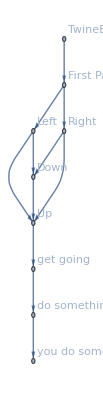

```mathematica
GraphicsRow[{twineGraph, twineAssoc}]
```

```mathematica
VertexList[twineGraph]
```

{TwineBridge_Test,First Passage,Left,Right,Up,Down,get going,do something,you do something}

```mathematica
EdgeList[twineGraph]
```

{TwineBridge_Test->First Passage,First Passage->Left,First Passage->Right,Left->Up,Left->Down,Right->Up,Right->Down,Up->get going,Down->Up,get going->do something,do something->you do something}

```mathematica
exportTwineProject[twineAssoc,"~/Desktop/correctExport" ]
```

~/Desktop/correctExport.html

Need some way to place the positions. Some function of the pid’s perhaps (but) before that, export needs to work on a graph.

#### Generate graphs from associations? | Yes by Normal;

Really, the question is can you compose Twine Story Structure from a graph.
So first, let’s compose a graph — write it explicitly to follow TwineStory Structure. (Remember VertexList and EdgeList)

Graph[{... twinestructure ...}]

Also, should I allow one to compose the story via text? for example:

“
PassageName:My Story, PassageContent: Welcome, [[First Passage]]
PassageName:First Passage, PassageContent:This is My First Passage. Go to the [[Second]]
PassageName:Second, PassageContent:This is the second passage.”

#### Let’s just define a graph, then go from there

Perhaps the use-case / workflow can be refined later. Right now, I just want to create a way to export a graph to a Twine Story.

The first node in the graph will be the story-title, i.e. the start of your story. Each node will hold a title and content

#### String Representation?

```mathematica
{storyTitle, passage1, passage2, passage3}= {"Test Story | [[First Passage]]", "First Passage | Welcome to Passge 1, let's go to Passage [[Two]]", "Two | Welcome to Passage 2, let's go to passage [[Three]]", "Three | Here is passage 3!"}
```

{Test Story | [[First Passage]],First Passage | Welcome to Passge 1, let's go to Passage [[Two]],Two | Welcome to Passage 2, let's go to passage [[Three]],Three | Here is passage 3!}

```mathematica
StringCases[%1448, StartOfString~~s___ ~~" |" :> s]
```

{{Test Story},{First Passage},{Two},{Three}}

```mathematica
StringCases[%1448, " | " ~~s___ :> s]
```

{{[[First Passage]]},{Welcome to Passge 1, let's go to Passage [[Two]]},{Welcome to Passage 2, let's go to passage [[Three]]},{Here is passage 3!}}

#### Association Representation

```mathematica
testAssociation
```

<|TwineBridge_Test→Start Here,First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

Define the story as an Association — Then display it s a graph

```mathematica
testingAssoc =<|"Other Story" -> "Start Here","Two" -> "Go to passage [[Three]]", "Three" ->  "Here we are at Passage Three"|>
```

<|Other Story→Start Here,Two→Go to passage [[Three]],Three→Here we are at Passage Three|>

```mathematica
Clear[twineWL]
twineWL[userAssoc_, outputForm_:"Summary"]:=Module[{assoc = userAssoc, rootNode, passageEdges,psgContent},
rootNode ={First[Keys[assoc]]-> Keys[assoc]⟦2⟧};
passageEdges =DeleteCases[Table[generateEdges[Keys[assoc]⟦index⟧,extractLinks[assoc⟦index⟧]], {index, 1, Length[assoc],1}], {}];
psgContent =Table[generateEdges[Keys[assoc]⟦index⟧,assoc⟦index⟧], {index, 1, Length[assoc],1}];
Switch[outputForm,
"Summary", GraphicsRow[{Framed@Column[Framed/@psgContent ], Graph[Flatten[rootNode~Join~passageEdges], VertexLabels->"Name"]}],
"Export",
If[DirectoryQ[FileNameJoin[{NotebookDirectory[], "TwineStories"}]],
Block[{twineFolder},
twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
exportTwineProject[assoc, twineFolder <> "/"<> ToString[First[Keys[assoc]]]]
],
Block[{twineFolder},
twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
CreateDirectory[twineFolder];
exportTwineProject[assoc, twineFolder <> "/"<> ToString[First[Keys[assoc]]]]]
];
]
]
```

```mathematica
twineWL[testingAssoc, "Export"]
```